```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA",
ExcludeParticles->{S[1],V[1],V[2],V[3],V[4],U[1],U[2],U[3],U[4],U[5],F[14]},InsertionLevel-> {Particles},GenericModel->"../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA_FC"
];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
tops = CreateTopologies[1,1->3,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT = { F[14]} -> { F[13],F[12],-F[12]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},
ExcludeParticles->{V[1],V[2],V[3],V[4],U[1],U[2],U[3],U[4],U[5],F[14],S[3],S[2],S[4]},
ExcludeFieldPoints-> {FieldPoint[_][F[14],S[4],-F[13]],FieldPoint[_][F[14],S[1],-F[13]],FieldPoint[_][S[4],S[1],S[1]],FieldPoint[_][S[4],S[4],S[1]],FieldPoint[_][S[1],S[1],S[1]],FieldPoint[_][S[4],S[4],S[4]],FieldPoint[_][F[14],S[1],S[1],-F[13]]}];
```

generic model {../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA_FC} initialized

classes model {../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA} initialized

in total: 2 Particles insertions

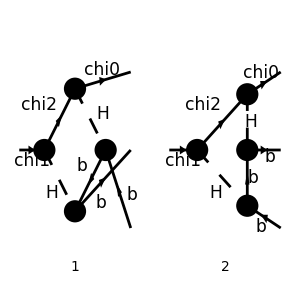

```mathematica
(* goodDiags=DiagramExtract[allDiags,{2,3}];*)
goodDiags=allDiags;
Paint[allDiags,ColumnsXRows->{2,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False,GaugeRules->{GaugeXi[S[_]]->1}]/.{SUNT->FASUNT},IncomingMomenta->{p},LorentzIndexNames->{μ,ν},OutgoingMomenta->{k1,k2,k3},LoopMomenta->{q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{a,b,c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[DiracSimplify[SUNSimplify[DiracSimplify[ampA]]]]
```

in total: 2 Particles amplitudes

1/4 sina^2 (sina^2-1) yb^2 ychi1x3 ychi2x3 δ_c1c2 (M2 (φ(k1,M0)).(φ(p,M1))+(φ(k1,M0)).(γ·q).(φ(p,M1))) (((φ(k2,MB)).(γ·k1).(φ(-k3,MB))-(φ(k2,MB)).(γ·q).(φ(-k3,MB))+2 MB (φ(k2,MB)).(φ(-k3,MB)))/((q^2-M2^2).((k1-q)^2-MH^2).((k1+k2-q)^2-MB^2).((k1+k2+k3-q)^2-MH^2))+(-(φ(k2,MB)).(γ·k1).(φ(-k3,MB))+(φ(k2,MB)).(γ·q).(φ(-k3,MB))+2 MB (φ(k2,MB)).(φ(-k3,MB)))/((q^2-M2^2).((k1-q)^2-MH^2).((k1+k3-q)^2-MB^2).((k1+k2+k3-q)^2-MH^2)))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, the t - t - g - g vertex only contributes when all external particles are on - shell, so we make use of this to simplify the final expressions

```mathematica
FCClearScalarProducts[];
SetMandelstam[k23,k13,k12,p,-k1,-k2,-k3,M1,M0,0,0];
```

```mathematica
ampEsimp2=ChangeDimension[Simplify[DiracSimplify[ampEsimp]/.{k12->M1^2+M0^2-k23-k13,MB->0}],4];
```

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,PaVe}];
Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]]]},{i,1,Length[lInts]}]
```

(D_1(k13,M0^2,k23,0,0,M1^2,0,M2^2,MH^2,MH^2) | 0
D_1(M0^2,M1^2,0,0,k23,-k13-k23+M0^2+M1^2,MH^2,M2^2,MH^2,0) | 0
D_00(0,0,M0^2,M1^2,k23,k13,MH^2,0,MH^2,M2^2) | 0
D_00(0,0,M0^2,M1^2,k23,-k13-k23+M0^2+M1^2,MH^2,0,MH^2,M2^2) | 0
D_11(k13,M0^2,k23,0,0,M1^2,0,M2^2,MH^2,MH^2) | 0
D_11(M0^2,M1^2,0,0,k23,-k13-k23+M0^2+M1^2,MH^2,M2^2,MH^2,0) | 0
D_12(0,k13,M0^2,k23,M1^2,0,MH^2,0,M2^2,MH^2) | 0
D_12(0,M1^2,M0^2,0,k13,k23,0,MH^2,M2^2,MH^2) | 0
D_12(0,M1^2,M0^2,0,-k13-k23+M0^2+M1^2,k23,0,MH^2,M2^2,MH^2) | 0
D_12(0,-k13-k23+M0^2+M1^2,M0^2,k23,M1^2,0,MH^2,0,M2^2,MH^2) | 0)

```mathematica
FullSimplify[ampEsimp2]
```

1/4 ⅈ π^2 sina^2 (sina^2-1) yb^2 ychi1x3 ychi2x3 δ_c1c2 (-D_00(0,0,M0^2,M1^2,k23,-k13-k23+M0^2+M1^2,MH^2,0,MH^2,M2^2) (φ(OverBar[k2])).(γ̄)^($AL($238)).(φ(-OverBar[k3])) (φ(OverBar[k1],M0)).(γ̄)^($AL($238)).(φ(p̄,M1))+D_00(0,0,M0^2,M1^2,k23,k13,MH^2,0,MH^2,M2^2) (φ(OverBar[k2])).(γ̄)^($AL($242)).(φ(-OverBar[k3])) (φ(OverBar[k1],M0)).(γ̄)^($AL($242)).(φ(p̄,M1))+(φ(OverBar[k2])).(γ̄·OverBar[k1]).(φ(-OverBar[k3])) ((φ(OverBar[k1],M0)).(φ(p̄,M1)) ((M0+M2) D_1(k13,M0^2,k23,0,0,M1^2,0,M2^2,MH^2,MH^2)-(M0+M2) D_1(M0^2,M1^2,0,0,k23,-k13-k23+M0^2+M1^2,MH^2,M2^2,MH^2,0)+M0 (D_11(k13,M0^2,k23,0,0,M1^2,0,M2^2,MH^2,MH^2)-D_11(M0^2,M1^2,0,0,k23,-k13-k23+M0^2+M1^2,MH^2,M2^2,MH^2,0)))+(D_12(0,M1^2,M0^2,0,-k13-k23+M0^2+M1^2,k23,0,MH^2,M2^2,MH^2)-D_12(0,M1^2,M0^2,0,k13,k23,0,MH^2,M2^2,MH^2)) (φ(OverBar[k1],M0)).(γ̄·OverBar[k2]+γ̄·OverBar[k3]).(φ(p̄,M1))+D_12(0,-k13-k23+M0^2+M1^2,M0^2,k23,M1^2,0,MH^2,0,M2^2,MH^2) (φ(OverBar[k1],M0)).(γ̄·OverBar[k2]).(φ(p̄,M1))-D_12(0,k13,M0^2,k23,M1^2,0,MH^2,0,M2^2,MH^2) (φ(OverBar[k1],M0)).(γ̄·OverBar[k3]).(φ(p̄,M1))))

```mathematica
ampSquared= FermionSpinSum[(ampEsimp2 (ComplexConjugate[ampEsimp2])),ExtraFactor->1/2]//DiracSimplify//Simplify;
```

```mathematica
Collect[ampSquared,{PaVe},Simplify]
```

```mathematica
ampSquared/.{k12->0.21,k23->300.,k13->250.,M1->100.,M2->110.,MH->125.0,M0->90.0}
```

-1/8 π^4 sina^4 (sina^2-1)^2 yb^4 ychi1x3^2 ychi2x3^2 (-8.75716×10^16 (D_1(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.))^2-400. (-4.37858×10^14 D_1(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0)-2.42796×10^9 D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.)+2.42796×10^9 D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.)+1.97036×10^14 D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.)-1.97036×10^14 D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0)-7.03148×10^12 D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.)-1.11606×10^13 D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.)+1.11606×10^13 D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.)+4.12914×10^12 D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.)) D_1(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.)-8.75716×10^16 (D_1(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0))^2+3.25867×10^8 (D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.))^2+3.25867×10^8 (D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.))^2-1.77332×10^16 (D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.))^2-1.77332×10^16 (D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0))^2+4.80044×10^15 (D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.))^2+1.92599×10^16 (D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.))^2+1.92599×10^16 (D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.))^2+4.82946×10^15 (D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.))^2-6.51735×10^8 D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.) D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.)+4.37033×10^11 D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.) D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.)-4.37033×10^11 D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.) D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.)-4.37033×10^11 D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.) D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0)+4.37033×10^11 D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.) D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0)+3.54665×10^16 D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.) D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0)+2.5016×10^12 D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.) D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.)-2.5016×10^12 D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.) D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.)+1.26567×10^15 D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.) D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.)-1.26567×10^15 D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0) D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.)+5.01333×10^12 D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.) D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.)-5.01333×10^12 D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.) D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.)+2.00891×10^15 D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.) D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.)-2.00891×10^15 D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0) D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.)+1.92309×10^16 D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.) D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.)-5.01333×10^12 D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.) D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.)+5.01333×10^12 D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.) D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.)-2.00891×10^15 D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.) D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.)+2.00891×10^15 D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0) D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.)-1.92309×10^16 D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.) D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.)-3.85199×10^16 D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.) D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.)-2.51173×10^12 D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.) D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.)+2.51173×10^12 D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.) D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.)-7.43244×10^14 D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.) D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.)+7.43244×10^14 D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0) D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.)-9.63004×10^15 D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.) D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.)-1.9289×10^16 D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.) D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.)+1.9289×10^16 D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.) D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.)+400. D_1(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0) (-2.42796×10^9 D_00(0,0,8100.,10000.,300.,250.,15625.,0,15625.,12100.)+2.42796×10^9 D_00(0,0,8100.,10000.,300.,17550.,15625.,0,15625.,12100.)+6.11534×10^7 (3.222×10^6 D_11(250.,8100.,300.,0,0,10000.,0,12100.,15625.,15625.)-3.222×10^6 D_11(8100.,10000.,0,0,300.,17550.,15625.,12100.,15625.,0)-114981. D_12(0,250.,8100.,300.,10000.,0,15625.,0,12100.,15625.)-182502. D_12(0,10000.,8100.,0,250.,300.,0,15625.,12100.,15625.)+182502. D_12(0,10000.,8100.,0,17550.,300.,0,15625.,12100.,15625.)+67521. D_12(0,17550.,8100.,300.,10000.,0,15625.,0,12100.,15625.)))) δ_c1c2^2